# Plot Spectrum

## A Mathematica Notebook to easily plot a spectrum from CSV files containing transition energies and intensities (oscillator strengths), typically results from Time-Dependent Quantum Chemistry calculations.

Author Carlos Eduardo Vieira de Moura (carlosevmoura@iq.ufrj.br)

## Definitions and Functions

### Working directory definition (You should define this one!)

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/carlos/Documents/GitHub/CompChemTools/graphics

### PeakGen: Generate an Gaussian Distribution upon a given transition #1: Amplitude (Oscillator Strength) #2: Transition Energy #3: Standard Deviation (StDev variable) #4: Dimension (Recommended: x)

```mathematica
PeakGen:=#1PDF[NormalDistribution[#2,#3],#4]*0.525&
```

### TotalPeaksGen: #1: Dimension (Recommended: x) #2: Variable containing data from CSV file #3: Standard Deviation (StDev variable)

```mathematica
TotalPeaksGen:=
Total[
Table[
PeakGen[#2[[i,2]],#2[[i,1]],#3,#1],
{i,Length[#2]}
]
]&
```

### PlotTotalPeaks: #1: Variable containing data from CSV file #2: Standard Deviation (StDev variable) #3: Minimum value for x axis in the plot #4: Maximum value for x axis in the plot #5: Line color #6: Legends

```mathematica
PlotTotalPeaks:=
Plot[TotalPeaksGen[x,#1,#2],{x,#3,#4},
PlotRange->All,
Frame->True,
FrameLabel->{Style["Energy (eV)",FontSize->16],Style["Oscillator Strength",FontSize->16]},
PlotStyle->Directive[#5],
FrameTicksStyle->Directive[FontSize->14],
ImageSize->500,
PlotLegends->{#6}]&
```

### ListPlotPeaks: #1: Variable containing data from CSV file #2: Line color

```mathematica
ListPlotPeaks:=
ListPlot[#1,
Filling->Axis,
PlotStyle->Directive[PointSize[Medium],#2],
ImageSize->500]&
```

### DeleteHeader: Remove the reader from CSV file

```mathematica
DeleteHeader:=Delete[#,1]&
```

### XMin & XMax: Minimum and maximum values from x variable in the plot

```mathematica
XMinGen:=Floor[Min[#[[All,1]]]-1]&
XMaxGen:=Ceiling[Max[#[[All,1]]]+1]&
```

### StDev: Minimum and maximum values from x variable in the plot

```mathematica
StDev=0.15;
```

### Defining Apple Colors in Mathematica

```mathematica
blue=RGBColor[17.6/100,41.6/100,63.1/100];
green=RGBColor[34.9/100,66.7/100,33.3/100];
yellow=RGBColor[96.9/100,68.6/100,20.8/100];
red=RGBColor[86.3/100,13.3/100,19.6/100];
brown=RGBColor[58.4/100,38.8/100,23.9/100];
purple=RGBColor[55.3/100,27.5/100,55.7/100];
grey=RGBColor[55.7/100,57.3/100,56.9/100];
apple8={blue,green,yellow,Orange,red,brown,purple,grey};
```

## How to use this notebook?

## 1) Evaluate all cells contained in Definitions and Funcions Chapter - You can also copy this functions to other working notebook, as you prefer; - Modifications can be made, according to your needs;

## 2) Import and save your data in a variable; - Use Import function combined with DeleteHeader;

## 3) Apply PlotTotalPeaks and ListPlotPeaks to build plots - Define all variables needed by these functions; - Use Show function to show both plots together;

## Usage Example

thiopheneData: Results for C_4 H_4 S at TD-B3LYP level with 6-31+G* basis set

### Importing data

```mathematica
thiopheneData=Import["auxiliary files/thiophene-tddft.csv","CSV"]//DeleteHeader
```

{{5.705,0.1021},{5.7465,0.0073},{5.8036,0.0883},{5.9727,0.},{6.0481,0.},{6.4087,0.0007},{6.6331,0.0225},{6.6518,0.},{6.7855,0.},{7.0236,0.0321},{7.0997,0.},{7.2338,0.0003},{7.3128,0.077},{7.3567,0.},{7.3665,0.3062},{7.438,0.0012},{7.5818,0.0646},{7.65,0.0005},{7.8217,0.0017},{7.831,0.0014},{7.8899,0.},{8.2053,0.0001},{8.2861,0.0052},{8.5289,0.},{8.6386,0.},{8.6533,0.0021},{8.6919,0.0009},{8.7098,0.0001},{8.8503,0.0021},{8.8879,0.}}

### Plotting spectrum using XMinGen and XMaxGen to obtain automatically plot borders

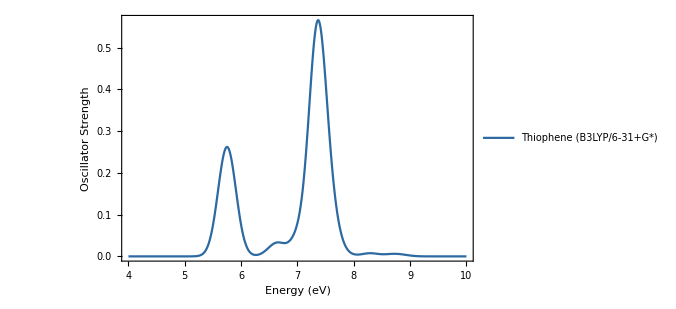

```mathematica
PlotTotalPeaks[thiopheneData,StDev,XMinGen[thiopheneData],XMaxGen[thiopheneData],apple8[[1]],"Thiophene (B3LYP/6-31+G*)"]
```

### You can also apply PlotTotalPeaks setting values for stardard deviation and also minimum and maximum for x axis, for example

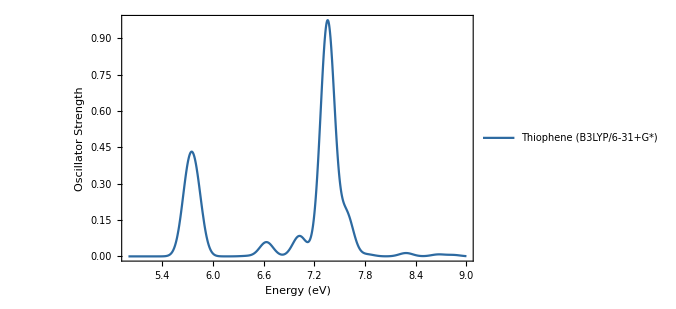

```mathematica
thiophenePlot=PlotTotalPeaks[thiopheneData,0.08,5.0,9.0,apple8[[1]],"Thiophene (B3LYP/6-31+G*)"]
```

### Plotting peaks for a clear visualization of computational chemistry results

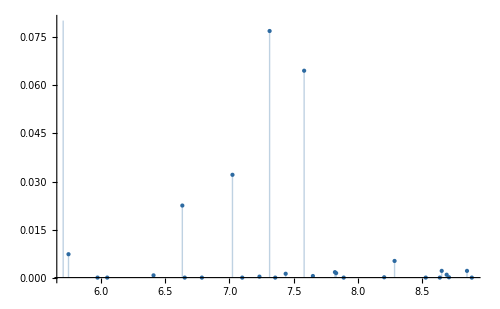

```mathematica
thiophenePeaks=ListPlotPeaks[thiopheneData,apple8[[1]]]
```

### Showing both plots in one graphic

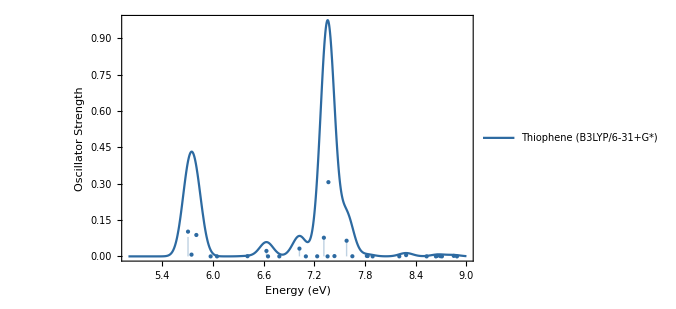

```mathematica
Show[thiophenePlot,thiophenePeaks]
```

# Enjoy!